```mathematica
μextreme[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/uh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[us_,uh_,μ_,z_,θ_]:=us^(θ/2-z)Sqrt[1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z))]/(μ(1-(us/uh)^(z-θ)));
uz1[q_,us_,uh_,μ_,z_,θ_]:=NDSolveValue[
{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) (((-2-z+θ) u[t]^(3-2 z) (u[t]/uh)^(z-θ))/uh^2-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(3-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(3-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)+(2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+((-((2+z-θ) (u[t]/uh)^(1+z-θ))/uh-(uh^(-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(1+2 z-2 θ) (u[t]/uh)^(-z+θ))/(2 (-2+θ))+(uh^(-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(1+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2-θ)) u'[t]^2)/(-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^(3-2 z) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]== us,u'[0]==0},u,{t,0.1,5.5}
];
fu1[t_,q_,us_,uh_,μ_,z_,θ_]:=uz1[q,us,uh,μ,z,θ][t];
dfu1[t_,q_,us_,uh_,μ_,z_,θ_]:=D[uz1[q,us,uh,μ,z,θ][t1],t1]/.{t1->t};
pu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
Return[u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
```

```mathematica
βpu[t_,q_,us_,uh_,μ_,z_,θ_]:=Block[
{du,u,fu,β},
du=dfu1[t,q,us,uh,μ,z,θ];
u=fu1[t,q,us,uh,μ,z,θ];
fu=1-(us/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) us^(2(z-θ+1))/uh^(2z-2θ)(1-(us/uh)^(θ-z));
β=1/(D[1-(u1/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) u1^(2(z-θ+1))/uh^(2z-2θ)(1-(u1/uh)^(θ-z)),u1]/.{u1-> us});
Return[β u^(θ/2-1)du/(fu Sqrt[u^(2(1-z))fu - du^2/fu])];
];
```

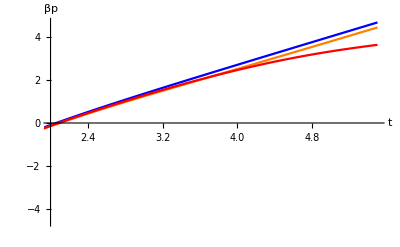

```mathematica
Show[
ListLinePlot[Table[{i,-(Abs[βpu[i,0.500qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,0.1,5.5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,-(Abs[βpu[i,0.970qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,0.1,5.5,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,-(Abs[βpu[i,0.996qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]]//Log)},{i,0.1,5.5,0.05}],PlotStyle->Red],
PlotRange->{{2,5.5},All},AxesOrigin->{2,0},AxesLabel->{t,βp}
]
```

```mathematica
Print[Table[{i,βpu[i,2.5qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]},{i,0.1,5.5,0.05}]]
```

{{0.1,-68.2738},{0.15,-74.3556},{0.2,-70.1009},{0.25,-60.7688},{0.3,-49.4291},{0.35,-37.7232},{0.4,-26.2603},{0.45,-14.9977},{0.5,-3.70843},{0.55,7.6232},{0.6,18.8861},{0.65,30.1911},{0.7,41.7574},{0.75,53.4507},{0.8,64.3444},{0.85,72.3569},{0.9,73.7757},{0.95,62.3659},{1.,30.6193},{1.05,-16.7438},{1.1,-54.9806},{1.15,-71.9976},{1.2,-73.7281},{1.25,-67.2561},{1.3,-56.9653},{1.35,-45.3728},{1.4,-33.724},{1.45,-22.3551},{1.5,-11.1036},{1.55,0.212978},{1.6,11.5269},{1.65,22.7782},{1.7,34.1564},{1.75,45.8138},{1.8,57.3867},{1.85,67.5888},{1.9,73.8466},{1.95,71.6876},{2.,53.935},{2.05,14.9667},{2.1,-32.2032},{2.15,-63.1243},{2.2,-73.906},{2.25,-72.1456},{2.3,-63.9701},{2.35,-53.0171},{2.4,-41.3179},{2.45,-29.7627},{2.5,-18.4639},{2.55,-7.19859},{2.6,4.13396},{2.65,15.4201},{2.7,26.6857},{2.75,38.1597},{2.8,49.8682},{2.85,61.1698},{2.9,70.3773},{2.95,74.3562},{3.,67.7447},{3.05,42.7821},{3.1,-1.84244},{3.15,-45.4365},{3.2,-68.7773},{3.25,-74.3411},{3.3,-69.8177},{3.35,-60.3653},{3.4,-48.9896},{3.45,-37.2872},{3.5,-25.8352},{3.55,-14.5753},{3.6,-3.2829},{3.65,8.04759},{3.7,19.3083},{3.75,30.6198},{3.8,42.197},{3.85,53.8832},{3.9,64.7147},{3.95,72.5593},{4.,73.628},{4.05,61.5781},{4.1,29.0102},{4.15,-18.5049},{4.2,-55.9938},{4.25,-72.2863},{4.3,-73.5985},{4.35,-66.9184},{4.4,-56.5425},{4.45,-44.9321},{4.5,-33.2922},{4.55,-21.9322},{4.6,-10.6803},{4.65,0.638753},{4.7,11.95},{4.75,23.2014},{4.8,34.5891},{4.85,46.2545},{4.9,57.8062},{4.95,67.9161},{5.,73.9537},{5.05,71.3561},{5.1,52.8576},{5.15,13.1765},{5.2,-33.7595},{5.25,-63.8528},{5.3,-74.0189},{5.35,-71.9257},{5.4,-63.5924},{5.45,-52.5828},{5.5,-40.879}}

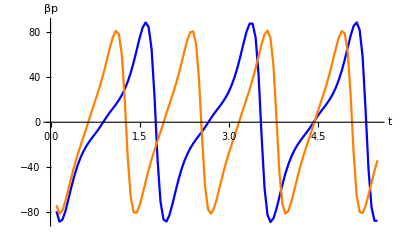

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,1.5qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]},{i,0.1,5.5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,βpu[i,2.0qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.1,1,0.75μextreme[1,1,0],1,0]},{i,0.1,5.5,0.05}],PlotStyle->Orange],
PlotRange->{{0.0,5.5},All},AxesOrigin->{0,0},AxesLabel->{t,βp}
]
```

```mathematica
Reduce[
2(2-θ)(2+z-θ)rh/(z-θ)≥0&&(z-1+θ/2)/2/(2-θ)≥0&&rh>0,{rh,θ,z}
]
```

rh>0&&((θ<2/3&&z≥(2-θ)/2)||(2/3≤θ<2&&z>θ))

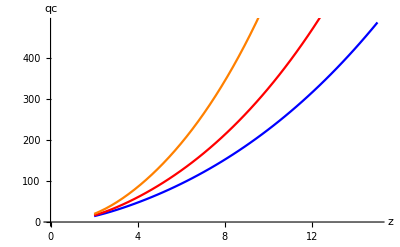

```mathematica
Block[
{qcrit,μextreme},
μextreme[rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[rs_,rh_,μ_,z_,θ_]:=Sqrt[1-(rh/rs)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/rs^(2(z-θ+1))(1-(rh/rs)^(θ-z))]/(μ rs(1-(rh/rs)^(z-θ)));
Print[
Show[
Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1.0],z,1.0],{z,2,15},AxesLabel->{z,qc},AxesOrigin->{0,0},PlotStyle->Blue],
Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1.2],z,1.2],{z,2,15},AxesLabel->{z,qc},AxesOrigin->{0,0},PlotStyle->Red],
Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1.4],z,1.4],{z,2,15},AxesLabel->{z,qc},AxesOrigin->{0,0},PlotStyle->Orange]
]
];
]
```